# Thunderstorm Analyzer

ABSTRACT:
The goal of this project is the creation of a system which will automatically get the data from public weather servers, analyze quantities like the number of cosmic rays, levels of ionizing radiation, electrostatic field strength, etc., and study their temporal correlation to detect the cases of Thunderstorm ground enhancements (TGE).
Thunderstorm ground Enhancement is a process of increase in the level of gamma radiation, number of electrons and neutrons, connected to the propagation of cosmic rays through strong atmospheric electric fields.
It was observed that during thunderstorms electrostatic field increases by orders of magnitude and gamma radiation levels as well as number of neutrons and relativistic electrons increase up to 10 times above cosmic ray background. When electrostatic field reaches certain levels lightning happens and the level of gamma radiation, electrons and neutrons as well as the field itself fall down immediately after the lightning.
The TGE events are characterized by following 7 criteria:

Large fluxes of electrons and gamma rays with durations around 10 minutes;

Increase in neutron number;

Microsecond electron bursts with around 50ms duration;

Increase of high energy muon level;

Large, usually negative, near-surface electric field, rising sometimes from deep negative to near zero positive values. Usually field is at the level of -10 - -30 kV/m;

Decrease of the cloud-ground lightnings and increase of intra-cloud lightnings.

Increase of relative humidity above 80% and decrease of air temperature below 5-6 degrease Celsius.

The system should analyze all the data and look for this kind of events and notify us upon their occurring.

## Import Weather Data from csv file.

#### Delete corrupted sublists and the first element of the list which contains header of csv file.

#### Data importer from csv file.

```mathematica
dataImporter[filePath_String, nOfColumns_Integer]:=Select[
	DeleteCases[
		Delete[
			Import[
				StringJoin[
					NotebookDirectory[], filePath
				]
			],
			1
		],
		"", {2}
	],
	(Length[#] == nOfColumns)&
];
```

#### Conversion rule for converting month names to month numbers.

```mathematica
monthRule:={"Jan"->1,"Feb"->2,"Mar"->3,"Apr"->4,"May"->5,"Jun"->6,"Jul"->7,"Aug"->8,"Sep"->9,"Oct"->10,"Nov"->11,"Dec"->12};
```

#### Transforms the date to the format of {y, m, d, h, m, s}

```mathematica
dateFormater[inputList_] := Replace[
	Part[
		MapAt[
			ToExpression,
			ReplaceAll[
				StringSplit[
					inputList,
					":" | " " | "-"
				],
				monthRule],
			{All,{1,2,3,4,5,6}}
		],All, {3, 2, 1, 4, 5, 6}
	],
	{year_, rest__} :> {year+2000, rest},
	{1}
];
```

### Import Electric Filed Data

```mathematica
electricFieldFull = dataImporter["Weather Data (05.Jul - 07.Jul.16)\\Electric_Field_MAKET.csv", 2];

electricFieldFullConverted = Transpose[{dateFormater[electricFieldFull[[All,1]]], electricFieldFull[[All,2]]}];
```

```mathematica
electricField = Part[
	electricFieldFullConverted,
	Position[
		electricFieldFullConverted,
		{2016, 7, 6, 06, 00, 00.}][[1, 1]] ;; Position[electricFieldFullConverted, {2016, 7, 6, 14, 00, 00.}][[1, 1]]
];
```

### Import STAND Electron and Gamma ray Detector Data

```mathematica
stand1Raw = dataImporter["Weather Data (05.Jul - 07.Jul.16)\\Stand_1cm.csv", 13];

stand1 = Transpose[{dateFormater[stand1Raw[[All,1]]],stand1Raw[[All,2]]}];
stand1Normalized = Transpose[{dateFormater[stand1Raw[[All,1]]],N[Rescale[stand1Raw[[All,2]],{Min[stand1],Max[stand1]},{0, 20}]]}];
```

### Import NaI Electron and Gamma ray Detector Data

```mathematica
naIFull = dataImporter["Weather Data (05.Jul - 07.Jul.16)\\NaI.csv",19];

naI3 = Transpose[
	{dateFormater[naIFull[[All, 1]]], naIFull[[All, 3]]}
];
```

### Import temperature and humidity data.

```mathematica
weatherData = Select[
	Delete[
		Import[
			StringJoin[NotebookDirectory[],"Weather Data (05.Jul - 07.Jul.16)\\Weather_Station.csv"]
		],
		1
	],
	(Length[#] == 37)&
];

weatherDataOrder = {
	{1,"Date/Time"},{2,"Outside Temperature"},{3,"Hi Temperature"},{4,"Low Temperature"},{5,"Outside Humidity"},
	{6,"Dew Point"},{7,"Wind Speed"},{8,"Wind Direction"},{9,"Wind Run"},{10,"Hi Wind Speed"},{11,"Hi Wind Direction"},
	{12,"Wind Chill"},{13,"Heat Index"},{14,"THW Index"},{15,"THWS Index"},{16,"Pressure"},{17,"Rain"},
	{18,"Rain Rate"},{19,"Solar Radiation"},{20,"Solra Energy"},{21,"Hi Solar Radiation"},{22,"UV Index"},{23,"UV Dose"},
	{24,"Hi UV"},{25,"Heating D-D"},{26,"Cooling D-D"},{27,"Inside Temperature"},{28,"Inside Humidity"},{29,"Inside Dew Point"},
	{30,"Inside Heat"},{31,"Inside EMC"},{32,"Inside Air Density"},{33,"ET"},{34,"Wind Samp"},{35,"Wind TX"},{36,"ISS Recept"},{37,"Arc Int\n"}
};

temperature = Transpose[{dateFormater[weatherData[[All, 1]]], weatherData[[All, 2]]}];
humidity = Transpose[{dateFormater[weatherData[[All, 1]]], weatherData[[All, 5]]}];
```

#### Generate the plot of electric field

```mathematica
(*plottingRange = {{{2016,8,1,11,00,00},{2016,8,1,12,00,00}},{-20,20}};*)
(*plottingRange = {{{2016,8,1,11,30,00},{2016,8,1,11,45,00}},{-20,20}};*)
plottingRange = Full;
```

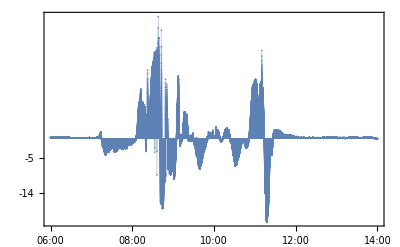

```mathematica
plotOriginal = DateListPlot[
	electricField,
	Filling->Axis,
	PlotRange->plottingRange,
	Joined->False,
	PlotTheme->"Detailed",
	FrameTicks->{{Range[-50,50,1],None},All}
]
```

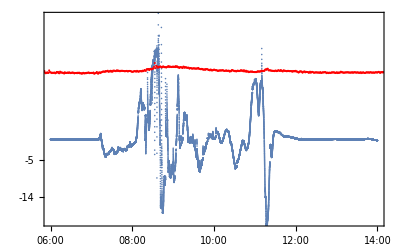

```mathematica
Show[DateListPlot[electricField,PlotRange->{-20,30},Joined->False,PlotTheme->"Detailed",
	FrameTicks->{{Range[-50,50,1],None},All}],DateListPlot[stand1Normalized,PlotRange->Full,PlotStyle->Red,Joined->False]]
```

#### Get local minima and maxima in time series

```mathematica
eFieldMaxs = Pick[
	electricField,
	PeakDetect[
		electricField[[All, 2]],
		100,
		0
	],
	1
];

eFieldMins = Pick[
	electricField,
	PeakDetect[
		-electricField[[All, 2]],
		100,
		0
	],
	1
];
```

#### Apply low cut filters to minima, maxima datasets.

```mathematica
eFieldMaxsFiltered = DeleteCases[
	eFieldMaxs,
	{date_,data_}/;data ≥ -0.5
];

eFieldMinsFiltered = DeleteCases[
	eFieldMins,
	{date_,data_}/;data ≥ -0.5
];
```

#### Construct a graph of a data with minimas and maximas.

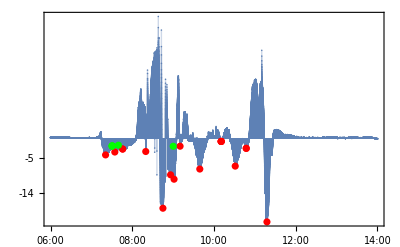

```mathematica
Show[
	plotOriginal,
	DateListPlot[
		eFieldMinsFiltered,
		PlotStyle->Red,
		PlotRange->plottingRange,
		Joined->False
	],
	DateListPlot[
		eFieldMaxsFiltered,
		PlotStyle->Green,
		PlotRange->plottingRange,
		Joined->False
	]
]
```

## Find the start and end of the peaks

```mathematica
eFieldPeakPosition=Flatten[Position[electricField, #]&/@eFieldMinsFiltered];
```

```mathematica
Part[electricField,#]&/@eFieldPeakPosition
```

{{{2016,7,6,7,20,48.},-4.26},{{2016,7,6,7,34,22.},-3.53158},{{2016,7,6,7,45,50.},-2.7775},{{2016,7,6,7,45,53.},-2.775},{{2016,7,6,8,19,48.},-3.4},{{2016,7,6,8,45,0.},-17.75},{{2016,7,6,8,56,15.},-9.295},{{2016,7,6,9,1,21.},-10.4071},{{2016,7,6,9,10,11.},-2.0575},{{2016,7,6,9,39,9.},-7.8375},{{2016,7,6,10,10,31.},-0.85},{{2016,7,6,10,10,32.},-0.85},{{2016,7,6,10,10,33.},-0.85},{{2016,7,6,10,10,34.},-0.85},{{2016,7,6,10,31,10.},-7.095},{{2016,7,6,10,47,20.},-2.6},{{2016,7,6,10,47,21.},-2.6},{{2016,7,6,11,17,45.},-21.21}}

```mathematica
(* Example of Function usage: moveToRight[electricField, eFieldPeakPosition, 2, 1200] *)
moveToRight[data_, peakPositions_, peakN_Integer, windowSize_Integer] := Select[
	Transpose[{
		Range[1,windowSize+1,30],
		TimeSeriesAggregate[
			Part[
				data[[All,2]],
				Span[Part[peakPositions,peakN], Part[peakPositions,peakN]+windowSize]
			],
			30
		]
	}],
	(#[[2]] ≤ 0)&
];
```

```mathematica
(* Example of Function usage: moveToLeft[electricField, eFieldPeakPosition, 2, 1200] *)
moveToLeft[data_, peakPositions_, peakN_Integer, windowSize_Integer] := Select[
	Transpose[{
		Range[-windowSize-1,-1,30],
		TimeSeriesAggregate[
			Part[
				data[[All,2]],
				Span[Part[peakPositions, peakN]-windowSize, Part[peakPositions, peakN]]
			],
			30
		]
	}],
	(#[[2]] ≤ 0)&
];
```

```mathematica
rightSlops=(moveToRight[electricField,eFieldPeakPosition,#,1200])&/@Range[1,Length[eFieldPeakPosition]];
leftSlops=(moveToLeft[electricField,eFieldPeakPosition,#,1200])&/@Range[1,Length[eFieldPeakPosition]];
```

```mathematica
rightEdge[data_, peakPositions_, peakN_Integer, windowSize_Integer] := Part[
	data,
	(Part[
		Select[
			moveToRight[data, peakPositions, peakN, windowSize],
			#[[2]]==Min[moveToRight[data, peakPositions, peakN, windowSize][[All,2]]]&
		],
		1,
		1
	] + peakPositions[[1]])
];
```

```mathematica
leftEdge[data_, peakPositions_, peakN_Integer, windowSize_Integer] := Part[
	data,
	(Part[
		Select[
			moveToLeft[data, peakPositions, 2, 1200],
			#[[2]]==Min[moveToLeft[data, peakPositions, peakN, windowSize][[All,2]]]&
		],
		1,
		1
	] + peakPositions[[1]])
];
```

## Filtering of data with a moving window.

## Detection of correlation between different time series.

## Detection of TGE events based on existing criteria.

## Detection of hidden correlations of atmospheric data with TGE events.

```mathematica
Partition
Split
```

Smoothing of the derivative of a gaussian